## Visualizing Functions

### One input one outputs: x_1→f(x_1) i.e f:ℝ→ℝ

There are lots of ways to plot a calculus one function with one input and one output

```mathematica
f[x1_]:= x1 +Sin[x1^2]
TabView[{
"Plot"->Plot[f[x1],{x1,-2,2}],
"ParPlot"->ParametricPlot[{x1,f[x1]},{x1,-2,2},Frame->True,GridLines->Automatic],
"ParPlotColor x"->ParametricPlot[{x1,f[x1]},{x1,-2,2},
Frame->True,PlotStyle->Thickness[0.01],GridLines->Automatic,
ColorFunction->Function[{x,f},Hue[x]]],
"ParPlotColor f"->ParametricPlot[{x1,f[x1]},{x1,-2,2},
Frame->True,PlotStyle->Thickness[0.01],GridLines->Automatic,
ColorFunction->Function[{x,f},Hue[f]]],
"Flat"->ParametricPlot[{x1,0},{x1,-2,2},
Frame->True,PlotStyle->Thickness[0.01],GridLines->Automatic,
ColorFunction->Function[x,Hue[f[x]]]]
},2]
```

12345

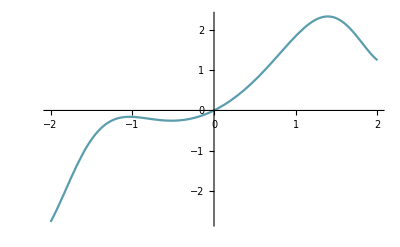

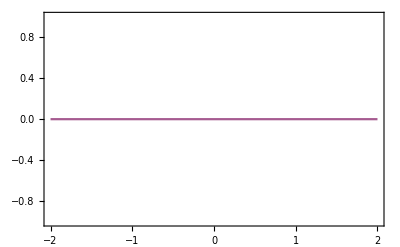

```mathematica
Plot[f[x1],{x1,-2,2},ColorFunction->Hue]
Plot[0,{x1,-2,2},Frame->True,ColorFunction->Function[x1,Hue[f[x1]]]]
```

```mathematica
f[{x1_,x2_}]:={x1 + 0.1x2 x1 ,x2+0.2Sin[x1 x2]}
TabView[{
"In"->ParametricPlot[{x1,x2},{x1,-2,2},{x2,-2,2},
Mesh->Automatic],
"Out"->ParametricPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},
Mesh->Automatic]
}]
```

12

### One input two outputs: x_1→{f1(x_1),f2(x_1)} i.e f:ℝ→ℝ^2

There are lots of ways to plot a calculus two function with one input and two outputs

```mathematica
f[x1_]:= {x1 +Sin[x1^2],Cos[x1]+x1}
TabView[{
"ParPlot"->ParametricPlot[f[x1],{x1,-2,2},Frame->True,GridLines->Automatic],
"ParPlotColor 1"->ParametricPlot[f[x1],{x1,-2,2},
Frame->True,PlotStyle->Thickness[0.01],GridLines->Automatic,
ColorFunction->Function[{x1,f1,f2},Hue[x1]]],
"ParPlotColor 2"->ParametricPlot[f[x1],{x1,-2,2},
Frame->True,PlotStyle->Thickness[0.01],GridLines->Automatic,
ColorFunction->Function[{x1,f1,f2},Hue[f1]]],
"ParPlotColor 3"->ParametricPlot[f[x1],{x1,-2,2},
Frame->True,PlotStyle->Thickness[0.01],GridLines->Automatic,
ColorFunction->Function[{x1,f1,f2},Hue[f2]]]
},1]
```

1234

```mathematica
Plot[f[x1],{x1,-2,2},ColorFunction->Hue]
Plot[0,{x1,-2,2},Frame->True,ColorFunction->Function[x1,Hue[f[x1]]]]
```

-Graphics-

-Graphics-

```mathematica
f[{x1_,x2_}]:={x1 + 0.1x2 x1 ,x2+0.2Sin[x1 x2]}
TabView[{
"In"->ParametricPlot[{x1,x2},{x1,-2,2},{x2,-2,2},
Mesh->Automatic],
"Out"->ParametricPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},
Mesh->Automatic]
}]
```

12

### One input three outputs: x_1→{f1(x_1),f2(x_1),f3(x1)} i.e f:ℝ→ℝ^3

There are lots of ways to plot a calculus three function with one input and three outputs

```mathematica
f[x1_]:= {x1 +Sin[x1^2],Cos[x1]+x1,-x1^2+ArcTan[Cos[1+x1^2]]}
TabView[{
"ParPlot3D"->ParametricPlot3D[f[x1],{x1,-2,2},FaceGrids->All],
"ParPlot3DColor 1"->ParametricPlot3D[f[x1],{x1,-2,2},
PlotStyle->Thickness[0.01],FaceGrids->All,
ColorFunction->Function[{x1,f1,f2,f3},Hue[x1]]],
"ParPlot3DColor 2"->ParametricPlot3D[f[x1],{x1,-2,2},
PlotStyle->Thickness[0.01],FaceGrids->All,
ColorFunction->Function[{x1,f1,f2,f3},Hue[f1]]],
"ParPlot3DColor 3"->ParametricPlot3D[f[x1],{x1,-2,2},
PlotStyle->Thickness[0.01],FaceGrids->All,
ColorFunction->Function[{x1,f1,f2,f3},Hue[f2]]],
"ParPlot3DColor 4"->ParametricPlot3D[f[x1],{x1,-2,2},
PlotStyle->Thickness[0.01],FaceGrids->All,
ColorFunction->Function[{x1,f1,f2,f3},Hue[f3]]],
"ParPlot Color f3"->ParametricPlot[f[x1][[1;;2]],{x1,-2,2},
PlotStyle->Thickness[0.01],GridLines->Automatic,
ColorFunction->Function[{x1},Hue[f[x1][[3]]]]]
},1]
```

```mathematica
123456
```

```mathematica
12345
```

```mathematica
Plot[f[x1],{x1,-2,2},ColorFunction->Hue]
Plot[0,{x1,-2,2},Frame->True,ColorFunction->Function[x1,Hue[f[x1]]]]
```

-Graphics-

-Graphics-

```mathematica
f[{x1_,x2_}]:={x1 + 0.1x2 x1 ,x2+0.2Sin[x1 x2]}
TabView[{
"In"->ParametricPlot[{x1,x2},{x1,-2,2},{x2,-2,2},
Mesh->Automatic],
"Out"->ParametricPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},
Mesh->Automatic]
}]
```

12

### Two input one outputs: {x_1,x_2}→f1(x_1,x_2) i.e f:ℝ^2→ℝ

There are lots of ways to plot a calculus three function with one input and three outputs

```mathematica
f[{x1_,x2_}]:= -x1^2+x2*ArcTan[Cos[1+x1^2+x2^2]]
TabView[{
"Plot3D"->Plot3D[f[{x1,x2}],{x1,-2,2},{x2,-2,2},FaceGrids->All],
"Plot3D Hue"->Plot3D[f[{x1,x2}],{x1,-2,2},{x2,-2,2},FaceGrids->All,ColorFunction->Function[{x1,x2,f},Hue[f]]],
"ContourPlot Hue"->ContourPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},ColorFunction->Hue,Contours->20],
"ContourPlot Default"->ContourPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},Contours->20]
},2]
```

1234

```mathematica
"ParPlot3DColor 1"->ParametricPlot3D[f[x1],{x1,-2,2},
PlotStyle->Thickness[0.01],FaceGrids->All,
ColorFunction->Function[{x1,f1,f2,f3},Hue[x1]]],
"ParPlot3DColor 2"->ParametricPlot3D[f[x1],{x1,-2,2},
PlotStyle->Thickness[0.01],FaceGrids->All,
ColorFunction->Function[{x1,f1,f2,f3},Hue[f1]]],
"ParPlot3DColor 3"->ParametricPlot3D[f[x1],{x1,-2,2},
PlotStyle->Thickness[0.01],FaceGrids->All,
ColorFunction->Function[{x1,f1,f2,f3},Hue[f2]]],
"ParPlot3DColor 4"->ParametricPlot3D[f[x1],{x1,-2,2},
PlotStyle->Thickness[0.01],FaceGrids->All,
ColorFunction->Function[{x1,f1,f2,f3},Hue[f3]]],
"ParPlot Color f3"->ParametricPlot[f[x1][[1;;2]],{x1,-2,2},
PlotStyle->Thickness[0.01],GridLines->Automatic,
ColorFunction->Function[{x1},Hue[f[x1][[3]]]]]
},1]
```

```mathematica
123456
```

```mathematica
12345
```

```mathematica
Plot[f[x1],{x1,-2,2},ColorFunction->Hue]
Plot[0,{x1,-2,2},Frame->True,ColorFunction->Function[x1,Hue[f[x1]]]]
```

-Graphics-

-Graphics-

```mathematica
f[{x1_,x2_}]:={x1 + 0.1x2 x1 ,x2+0.2Sin[x1 x2]}
TabView[{
"In"->ParametricPlot[{x1,x2},{x1,-2,2},{x2,-2,2},
Mesh->Automatic],
"Out"->ParametricPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},
Mesh->Automatic]
}]
```

12

### Two input two outputs: {x_1,x_2}→{f1(x_1,x_2),f2(x_1,x_2)} i.e f:ℝ^2→ℝ^2

There are a couple of ways to plot a calculus three function with two input and two outputs

```mathematica
f[{x1_,x2_}]:= {3+x1+0.2*Sin[x2 x2],1+x2-0.1 x1^2+0.2x2*ArcTan[x1+x2]}
p[r_,θ_]:=r{Cos[θ],Sin[θ]}
SqPic=ParametricPlot[{{x1,x2},f[{x1,x2}]},{x1,-2,2},{x2,-2,2},Mesh->Automatic,
MeshStyle->{Red, Blue}];
CirclePic=ParametricPlot[{p[r,θ],f[p[r,θ]]},{θ,0,2π},{r,0,2},Mesh->Automatic,MeshStyle->{Cyan, Black}];
TabView[{
"ParametricPlot Square"->SqPic,
"ParametricPlot Circle"->CirclePic,
"Together"->Show[CirclePic,SqPic]
},1]
```

123

### Three input three outputs: {x_1,x_2,x_3}→{f1(x_1,x_2,x_3),f2(x_1,x_2,x_3),f3(x_1,x_2,x_3)} i.e f:ℝ^3→ℝ^3

There are a couple of ways to plot a calculus three function with three input and three outputs

```mathematica
A=({{1.2, 3, 1}, {4.3, 2.4, -2}, {-3, 2, 4.5}});
p[r_,θ_,ϕ_]:=r{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]}
r=0.5;
ParametricPlot3D[{p[r,θ,ϕ],A.p[r,θ,ϕ]},{θ,0,2π},{ϕ,0,π},Mesh->Automatic,MeshStyle->{Red, Blue},PlotPoints->123,PlotRange->All]
```

-Graphics3D-

# First Return y'=f(y) e.g. y_1==0

The VDP system and the Rosseler system both cross y_1==0 repeatedly.  The first return map (fory_1==0) is a natural way to look at the behavior of the system as a map from the plane y_1=0 onto the plane y_1=0.

We are going to look at this first for the 2D VDP problem and then see how much messier it gets for the 3D Roseller system.

First Return Map (Informal Definition)
The first return map for an ODE y'=f(y) on a surface 𝒮  is where the solution of the  ODE first returns to the surface 𝒮   (in the same direction) as a function on 𝒮.

## First Return Map for VDP System y_1==0

Our VDP system is
	y1' | = | y2                               
y2' | = | μ(1-y1^2)y2-y1
I am going to look at initial conditions y_0=(0,x) and catch the output y_*=(0,r(x)) the first time it crosses y_1==0 heading in the same direction. In Mathematica there is a way to catch values from the ODE solver when it locates an event.

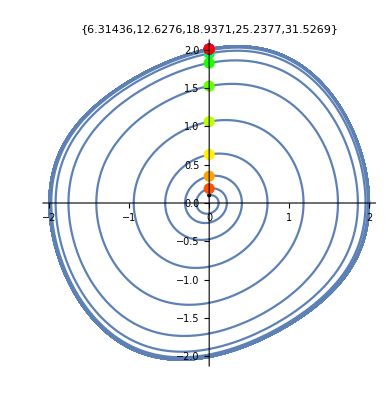

```mathematica
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
Df[μ_][{x_,v_}]:={{0,1},{-1-2v x μ,μ (1-x^2)}}
TMax=124.5;y0={0,.1};μ=0.2; ϵ=1;
{Hmm,{Data}}=Reap[{ySol,JSol}=NDSolveValue[{
y'[t]==f[μ][y[t]],y[0]==y0,
J'[t]==Df[μ][y[t]].J[t],J[0]=={{1,0},{0,1}}
},{y,J},{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦1⟧==0,"Direction"->1,
"EventAction":> Sow[{t, y[t], J[t]}]}];
];
ParametricPlot[ySol[t],{t,0, TMax},
Epilog->{{Black,Point[ySol[0]]},Table[{Hue[i/Length[Data]],PointSize[0.02],Point[Data⟦i,2⟧]},{i,Length[Data]}]},
PlotLabel->Data⟦1;;5,1⟧]
```

## First Return Map for Rosseller System y_1==0

The same trick for the  Rosseler system.

```mathematica
Clear[ f,df,y1,y2,y3,a,b,c]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={0.2,0.2,5.7};  TMax=54;
y0={0,1.7,14.6};
{Hmm,{Data}}=Reap[{ySol,JSol}=NDSolveValue[{
y'[t]==f[StdParams][y[t]],y[0]==y0,
J'[t]==df[StdParams][y[t]].J[t], J[0]==({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})
},{y,J},{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦1⟧==0,"Direction"->1,
"EventAction":> Sow[{t, y[t], J[t]}]}];
];
BasePic=Show[
ParametricPlot3D[ySol[t],{t,0, TMax},
PlotRange->All],
Graphics3D[{Black,PointSize[0.02],Point[ySol[0]]}],
Graphics3D[{Opacity[0.5],Yellow,Polygon[15{{0,-1,0},{0,1,0},{0,1,2},{0,-1,2}}]}]];
Dots=Graphics3D[{PointSize[0.02],Table[{Hue[i/Length[Data]],Point[Data⟦i,2⟧]},{i,Length[Data]}]},
Axes->True,BoxRatios->{1, 1, 1}];
TabView[{
"y"->BasePic,
"y+"->Show[BasePic,Dots,PlotLabel->Data⟦All,1⟧],
"Dots"->Dots
}]
```

123